# Demonstrações no Mathematica em uma Introdução à Teoria Quântica de Campos e Física de Partículas

## Um notebook dinâmico e educacional para TQC

Por Bruno Gehlen F . da Silva

## Capítulo #1: Introdução e Teoria

## Contexto Histórico

O século XX iniciou com a grande descoberta da física quântica por Max Planck e seus estudos sobre a quantização da matéria e o Corpo Negro, permitindo descrever várias oscilações de diferentes modos confinados em uma cavidade (explicando a Catástrofe do Ultravioleta). Albert Einstein interpretou essa quantização como partículas sem massa chamadas fótons e utilizou essas novas descobertas para determinar seus Coeficientes, além do famoso Efeito Fotoelétrico. Com este novo formalismo, é possível utilizar os operadores de Aniquilação e Criação em modos de energia (ou momento) e até mesmo encontrar a Taxa de Transição entre diferentes estados quânticos.

No mesmo século, também houve enormes avanços na área da relatividade: não há um referencial absoluto, a luz viaja a uma velocidade constante e, dependendo da velocidade do observador, diferentes grandezas físicas podem ser medidas. Descobriram-se observáveis invariantes de Lorentz (simétricos por todo o Grupo de Poincaré), pois já se sabia que rotações mantinham normas inalteradas, e agora haviam os Boosts de Lorentz. Também foi descoberto que esses boosts se reduzem às transformações de referencial de Galileu no regime das baixas energias (validando ainda a física clássica tradicional), e então passou-se a lidar com objetos traduzidos como campos e operadores invariantes sob todas essas transformações, sejam elas contínuas ou discretas no universo.

Hoje em dia, a humanidade já foi capaz de conciliar ambas as teorias na então chamada de Teoria Quântica de Campos (TQC), onde, diferente da mecânica quântica usual, a quantidade de partículas do sistema pode ser modificada ao longo dos processos, sendo assim a base para diversos sistemas de diferentes áreas da física moderna, como o estudo da Matéria Condensada e a Física de Partículas em si. A maneira como a TQC é construída permite que a matriz S (de espalhamento, “scattering”) seja utilizada de forma que, tomando que as interações ocorram em um tempo muito curto comparado o resto do espalhamento e tratando os campos como operadores que criam e/ou aniquilam partículas de certos estados, é possível descrever qualquer processo onde entrem n partículas e saiam m outras.

## Formalismo Rápido

Falando propriamente sobre nossa teoria, é necessário lembrar alguns aspectos básicos da Teoria Quântica de Campos. Após a chamada “segunda quantização”, onde são estabelecidas as relações de comutação locais (em tempos iguais) entre os operadores de criação/aniquilação e a normalização dos estados, além de também definir a ação desses operadores em um estado de uma partícula:

-Graphics-

define-se que n partículas podem simultaneamente ocupar um estado de momento p, resultando na soma direta dos espaços de Hilbert das i partículas, também chamado de espaço de Fock, permitindo agora a introdução de Campos Escalares Quânticos:

-Graphics-

que são soluções da equação de Klein-Gordon e portanto podem ser decompostos em ondas planas. Processos semelhantes se aplicam em Campos Spinoriais (que descrevem férmions), o que demanda um aprofundamento no estudo das representações do Grupo de Poincaré ISO(1,3) (possui rotações, boosts de Lorentz, inversão temporal e por paridade) e sobre o que são spinores em si, e Campos Tensoriais, como do fóton e do hipotético gráviton, que exigem bases com polarizações para cada um dos índices do objeto, relacionados com spin inteiro (bósons).

É possível então deduzir as Regras de Feynman, tanto no espaço de posição quanto de momento, que ajudam durante o já bem estabelecido formalismo de Diagramas de Feynman, estes sendo representações das séries perturbativas que surgem ao calcular as funções entre n-pontos de teorias interagentes:

-Graphics-                        -Graphics-

Toda a ideia de diagramas e funções de muitos pontos facilita os cálculos pois basta que todas as amplitudes (chance de um estado inicial chegar em um estado final) que podem fisicamente contribuir para o processo sejam somadas, além de sutilidades como soma sobre spins e polarizações . Além disso, é chegado um momento em que é necessário estudar o processo de Renormalização de teorias já que a inserção de loops nos diagramas, apesar de incrementar a precição, acaba criando divergências nos observáveis, o que certamente não é compatível com quase tudo observado no universo atual, e portanto é necessário deformar a teoria em uma certa escala e fazer modificações em passos intermediários dos cálculos de forma que os observáveis extraídos agora sejam finitos.

## Capítulo #2: Cálculos

## Primeiros Cálculos

Agora, iniciam-se os cálculos de alguns espalhamentos já conhecidos para avaliar a autenticidade da teoria descrita até aqui. Tomando o famoso Espalhamento de Møller, algo extremamente natural na eletrodinâmica quântica escalar, onde dois elétrons se aproximam e se repelem ao trocar um fóton:

-Graphics-

Pela Lagrangiana, nota-se que os diagramas possíveis são o canal-t e canal-u (e isso pode ser visto com o auxílio do pacote FeynArts), e então, definindo a contração de índices e grandezas necessárias (variáveis de Mandelstam) :

```mathematica
normLortz[x_,y_]:=(x[[1]]*y[[1]])-(x[[2]]*y[[2]])-(x[[3]]*y[[3]])-(x[[4]]*y[[4]]);
	(*com a assinatura da métrica Lorentziana dada por (+,-,-,-)*)
p1={p10,p11,p12,p13};
p2={p20,p21,p22,p23};
p3={p30,p31,p32,p33};
p4={p40,p41,p42,p43};
	(*definição dos 4-momentos inicialmente genéricos*)
```

```mathematica
sups1={e>0,g>0,λ>0,α==e^2/(4π),
normLortz[p1+p2,p1+p2]==s,
(*normLortz[p3+p4,p3+p4]==s,*)
normLortz[p1-p3,p1-p3]==t,
(*normLortz[p2-p4,p2-p4]==t,*)
normLortz[p1-p4,p1-p4]==u
(*normLortz[p2-p3,p2-p3]==u*)
};
	(*constante de acomplamento e variáveis de mandelstam; são as suposições que vão ser usadas nos cálculos*) 
sups2={
normLortz[p1+p3,p2+p4]==s-u,
(p12 p22+p13 p23-p10 (p20+p30)+p11 (p21+p31)+p12 p32+p13 p33-p20 p40-p30 p40+p21 p41+p31 p41+p22 p42+p32 p42+p23 p43+p33 p43)==s-t
};
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

loading generic model file /home/brunogehlen/Documentos/wolfram-qft/FeynArts-3.11/Models/QED.gen

> $GenericMixing is OFF

generic model {QED} initialized

loading classes model file /home/brunogehlen/Documentos/wolfram-qft/FeynArts-3.11/Models/QED.mod

> 7 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 1 vertices

> 3 counterterms of order 1

classes model {QED} initialized

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 0 Generic, 0 Classes insertions

> Top. 3: 1 Generic, 1 Classes insertions

> Top. 4: 1 Generic, 1 Classes insertions

in total: 2 Generic, 2 Classes insertions

> Top. 1 aebf/cedf/ef.m, 0 diagrams

> Top. 2 aebf/cfde/ef.m, 0 diagrams

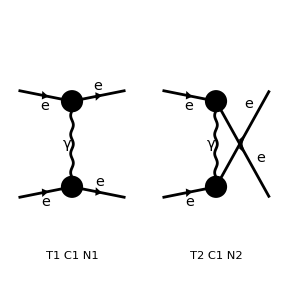

FeynArtsGraphics[{e,e}→{e,e}][([T1 C1 N1] | [T2 C1 N2]
Null | Null)]

```mathematica
<<<<FeynArts`;(*Carregamento do pacote FeynArts caso queira visualizar os diagramas*)
Paint[InsertFields[CreateTopologies[0,2->2],{F[1,{1}],F[1,{1}]}->{F[1,{1}],F[1,{1}]},Model->"QED",GenericModel->"QED"],ColumnsXRows->2,PaintLevel->{Classes}](*Utilizando o pacote FeynArts para ver os possíveis diagramas para um espalhamento férmions 2->2*)
```

além dos componentes da seção de choque:

```mathematica
vert[g_]:=ⅈ*g;
	(*Cada vértice dá um fator (-ⅈg)*)
propEsc[p_,m_]:=ⅈ/(normLortz[p,p]-m^2);
propFot[p_]:=-ⅈ/normLortz[p,p];
	(*O propagador depende do diagrama que contribue*)
mDiagramaQEDescalar[m_,g_,numVert_,numPropFot_,pIn_,pOut_,pPropg_]:=
(vert[g]^numVert)*
(propFot[pPropg]^numPropFot)*
(normLortz[pIn,pOut])*(ⅈ);
	(*Os fatores ⅈϵ foram retirados pois  e estamos no gauge de Feynman*)
	(*constantes como c e ℏ já estão definidos como 1*)
ℳQEDEsc=mDiagramaQEDescalar(*Um alias para diminuir o tamanho da função*);
```

```mathematica
crossSectionQEDCM[m_,g_,s_,t_,u_]:=(1/(64*π^2*normLortz[p1+p2,p1+p2]))*Abs[(ℳQEDEsc[m,g,2,1,p1+p2,p3+p4,p1+p2]*s)+(ℳQEDEsc[m,g,2,1,p1+p3,p2+p4,p1-p3]*t)+(ℳQEDEsc[m,g,2,1,p1+p4,p2+p3,p1-p4]*u)]^2;
(*O total será a soma das contribuções, e neste caso apenas os diagramas T e U*)
dσdΩ[m_,g_,s_,t_,u_]:=Simplify[Simplify[crossSectionQEDCM[m,g,s,t,u],Assumptions->sups1],Assumptions->sups2];
	(*Um alias para diminuir o tamanho da função, assumir acoplamentos positivos e assumir as variáveis de Mandelstam e suas relações*);
```

encontra - se que a seção de choque será dada por

```mathematica
secao=dσdΩ[Subscript[m, e],e,0,1,1]
```

(α^2 Abs[((t-u) (-s+t+u))/(t u)]^2)/(4 s)

condizente com a literatura! Escrevendo as variáveis de Mandelstam em função do ângulo

```mathematica
sups3={t->2(a^2)(Cos[θ]-1),u->2(a^2)(-Cos[θ]+1),α->1/137,s->4b^2};
```

é possível plotar a seção de choque no limite relativístico:

```mathematica
secaoplot=secao/.sups3;
Manipulate[Plot[secaoplot/.{a->p,b->ecm},{θ,0,π/2},PlotRange->{0,0.01},Frame->True,FrameLabel->{"Ângulo entre os eixos de p_1 e p_3","Seãço de Choque"},LabelStyle->Directive[Bold, 10],Ticks->Automatic,ImageSize->Large,GridLines->Automatic,PlotLabel->"Espalhamento elétron-elétron"],{{p,3},1,10},{{ecm,10},1,10}]
```

## Outros Campos

Para a QED com spinores, adiciona-se a nova regra para propagadores internos spinoriais, e novamente será possível ver por meio do FeynArts que somente o canal-s será possível. Tomando o Espalhamento Elétron-Muon:

-Graphics-

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 1 Generic, 1 Classes insertions

> Top. 3: 0 Generic, 0 Classes insertions

> Top. 4: 0 Generic, 0 Classes insertions

in total: 1 Generic, 1 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

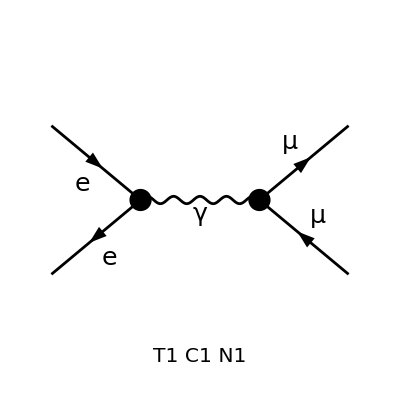

```mathematica
Paint[InsertFields[CreateTopologies[0,2->2],{F[1,{1}],-F[1,{1}]}->{F[1,{2}],-F[1,{2}]},Model->"QED"],ColumnsXRows->1,PaintLevel->{Classes}]
```

```mathematica
supSpin={e>0,g>0,λ>0,γ>0,
normLortz[p1+p2,p1+p2]==s,
(*normLortz[p3+p4,p3+p4]==s,*)
normLortz[p1-p3,p1-p3]==t,
(*normLortz[p2-p4,p2-p4]==t,*)
normLortz[p1-p4,p1-p4]==u,
(*normLortz[p2-p3,p2-p3]==u*)
Element[p1,Reals],Element[p2,Reals],Element[p3,Reals],Element[p4,Reals],
u*γ*vbar*ubar*γ*v==Sqrt[8*normLortz[]^2+normLortz[]^2+4*normLortz[]*()]
};
vertSpin[g_]:=ⅈ*g*γ;
mDiagramaQEDspinorial[g_,numVert_,numPropFot_,pPropg_,u_,v_,ubar_,vbar_]:=
(vertSpin[g]^numVert)*
(propFot[pPropg]^numPropFot)*
(vbar*u)*(ubar*v)*(ⅈ);
```

```mathematica
ℳ=mDiagramaQEDspinorial[e,2,1,p1+p2,u,v,ubar,vbar];
ℳDagger=mDiagramaQEDspinorial[e,2,1,p1+p2,ubar,vbar,u,v];
Simplify[(1/4)*(ℳ*ℳDagger),Assumptions->supSpin]
```

(2 e^4)/s^2

e é possível confirmar a amplitude por meio do pacote FeynRules:

```mathematica
CreateFeynAmp[InsertFields[CreateTopologies[0,2->2],{F[1,{1}],-F[1,{1}]}->{F[1,{2}],-F[1,{2}]},Model->"QED"]]
```

loading generic model file /home/brunogehlen/Documentos/wolfram-qft/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/brunogehlen/Documentos/wolfram-qft/FeynArts-3.11/Models/QED.mod

> 7 particles (incl. antiparticles) in 2 classes

> $CounterTerms are ON

> 1 vertices

> 3 counterterms of order 1

classes model {QED} initialized

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 1 Generic, 1 Classes insertions

> Top. 3: 0 Generic, 0 Classes insertions

> Top. 4: 0 Generic, 0 Classes insertions

in total: 1 Generic, 1 Classes insertions

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 1 Classes amplitudes

in total: 1 Generic, 1 Classes amplitudes

FeynAmpList[Process→{{F[1,{1}],p1,ME,-Charge},{-F[1,{1}],p2,ME,Charge}}→{{F[1,{2}],k1,MM,-Charge},{-F[1,{2}],k2,MM,Charge}},Model→{QED},GenericModel→{Lorentz},AmplitudeLevel→{Generic,Classes},ExcludeParticles→{},ExcludeFieldPoints→{},LastSelections→{}][FeynAmp[GraphID[Topology==1,Generic==1],Integral[],RelativeCF v̄[p2,Mass[F[1,{1}]]].(ga[Lor1].om_- G_FFV^(0)[ga[KI1[3]].om_-]+ga[Lor1].om_+ G_FFV^(0)[ga[KI1[3]].om_+]).u[p1,Mass[F[1,{1}]]] ū[k1,Mass[F[1,{2}]]].(ga[Lor2].om_- G_FFV^(0)[ga[KI1[3]].om_-]+ga[Lor2].om_+ G_FFV^(0)[ga[KI1[3]].om_+]).v[k2,Mass[F[1,{2}]]] g[Lor1,Lor2] 1/((k1+k2)^2-Mass[V[Gen5],Internal]^2),{Mass[F[1,{1}]],Mass[F[1,{1}]],Mass[F[1,{2}]],Mass[F[1,{2}]],Mass[V[Gen5],Internal],G_FFV^(0)[ga[KI1[3]].om_-],G_FFV^(0)[ga[KI1[3]].om_+],G_FFV^(0)[ga[KI1[3]].om_-],G_FFV^(0)[ga[KI1[3]].om_+],RelativeCF}→Insertions[Classes][{ME,ME,MM,MM,0,ⅈ EL,ⅈ EL,ⅈ EL,ⅈ EL,1}]]]

focando no termo de amplitude facilmente reconhecível: ("v")^("_")[...].("ga"["Lor"1].("om")_("-") G_FFV^(0)["ga"[KI1[3]].("om")_("-")]+"ga"["Lor"1].("om")_("+") G_FFV^(0)["ga"[KI1[3]].("om")_("+")])."u"[...] ("u")^("_")[...].("ga"["Lor"2].("om")_("-") G_FFV^(0)["ga"[KI1[3]].("om")_("-")]+"ga"["Lor"2].("om")_("+") G_FFV^(0)["ga"[KI1[3]].("om")_("+")])."v"[...] "g"["Lor"1,"Lor"2] 1/(("k"1+"k"2)^2-Mass[V["Gen"5],Internal]^2),
onde tem-se as partículas ("v")^("_"),v,("u")^("_") e u, além do propagador proporcional a s^(□2) e m^2. Novamente, plotando a seção de choque no limite relativístico:

```mathematica
secchoqmuon=(1/137^2)*(1/(4*a))*(1+Cos[θ]^2);
Manipulate[Plot[secchoqmuon/.{a->s},{θ,0,π/2},PlotRange->{0,0.00003},Frame->True,FrameLabel->{"Ângulo entre os eixos de p_1 e p_3","Seção de Choque"},LabelStyle->Directive[Bold, 10],Ticks->Automatic,ImageSize->Medium,GridLines->Automatic,PlotLabel->"Espalhamento elétron-múon"],{{s,1},0.01,7}]
```

Plotando outras seções de choque como a do Espalhamento Rutheford e Compton, tem-se:

```mathematica
secchoqruth=((α^2)/(4*a*Sin[θ/2]))*(b/a)*(Cos[θ/2]^2+((a-b)/mp)*Sin[θ/2]^2);
sups4={α->1/137,mp->938};
Manipulate[Plot[Evaluate[secchoqruth/.sups4]/.{a->ei,b->ef},{θ,0,π/2},PlotRange->{0,0.1},Frame->True,FrameLabel->{"Ângulo entre os eixos de p_1 e p_3","Seção de Choque"},LabelStyle->Directive[Bold, 10],Ticks->Automatic,ImageSize->Medium,GridLines->Automatic,PlotLabel->"Espalhamento Rutheford"],{ei,0.1,10},{{ef,7},0.1,10}]
```

```mathematica
secchoqcompt=((π*α^2)/(2*a^2))*(((1+Cos[θ])/(4))+((1)/((b^2/(2*a^2))+1+Cos[θ])));
sups5={α->1/137};
Manipulate[Plot[Evaluate[secchoqcompt/.sups5]/.{a->ω,b->m},{θ,0,π/2},Frame->True,FrameLabel->{"Ângulo entre os eixos de p_1 e p_3","Seção de Choque"},LabelStyle->Directive[Bold, 10],Ticks->Automatic,ImageSize->Medium,GridLines->Automatic,PlotLabel->"Espalhamento Compton"],{{ω,7},0.1,10},{m,0.1,10}]
```

Além disso, também é possível também calcular os possíveis decaímentos das partículas de uma lagrangiana em outras duas, por meio do pacote FeynRules, que possui essa funcionalidade nativamente, como pode ser visto:

```mathematica
$FeynRulesPath=SetDirectory[FileNameJoin[{NotebookDirectory[],"feynrules-current"}]](*Define-se o diretório do pacote FeynRules, documentado em seu site oficialhttps://feynrules.irmp.ucl.ac.be/Nonehttps://feynrules.irmp.ucl.ac.be/HyperlinkActionRecycledHyperlinkActive*);
<<FeynRules`(*Checa-se o bom carregamento do pacote (alguns erros podem aparecer, são ignoráveis)*);
SetDirectory[$FeynRulesPath<>"/Models/SM"](*Defin-se o diretório do modelo do Modelo Padrão*);
LoadModel["SM.fr"](*Carrega-se o modelo do Modelo Padrão*);
LoadRestriction["Massless.rst","DiagonalCKM.rst"](*Carrega-se as restrições do Modelo Padrão*);
FeynmanGauge=True;
```

- FeynRules -

Version: 2.3.49 ( 29 September 2021).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

This model implementation was created by

N. Christensen

C. Duhr

B. Fuks

Model Version: 1.4.7

http://feynrules.phys.ucl.ac.be/view/Main/StandardModel

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Standard Model loaded.

Loading restrictions from Massless.rst :  / 18

Loading restrictions from DiagonalCKM.rst :  / 3

Restrictions loaded.

```mathematica
decay=ComputeWidths[FeynmanRules[LSM]]
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Expanding the indices over 2 cores

Collecting the different structures that enter the vertex.

98 possible non-zero vertices have been found -> starting the computation:  / 98.

93 vertices obtained.

Flavor expansion of the vertices distributed over 2 cores:  / 93

Computing the squared matrix elements relevant for the 1->2 decays:

/ 40

{{{H,b,b^-},(3 (-4 MB^2+MH^2) √(-4 MB^2 MH^2+MH^4) yb^2)/(16 π Abs[MH]^3)},{{H,ta,ta^-},((MH^2-4 MTA^2) √(MH^4-4 MH^2 MTA^2) ytau^2)/(16 π Abs[MH]^3)},{{H,t,t^-},(3 (MH^2-4 MT^2) √(MH^4-4 MH^2 MT^2) yt^2)/(16 π Abs[MH]^3)},{{H,W^†,W},(e^4 √(MH^4-4 MH^2 M_W^2) (MH^4-4 MH^2 M_W^2+12 M_W^4) vev^2)/(256 M_W^4 π s_w^4 Abs[MH]^3)},{{Z,W^†,W},(c_w^2 e^2 √(-4 M_W^2 MZ^2+MZ^4) (-48 M_W^6-68 M_W^4 MZ^2+16 M_W^2 MZ^4+MZ^6))/(192 M_W^4 π s_w^2 Abs[MZ]^3)},{{H,Z,Z},(e^4 √(MH^4-4 MH^2 MZ^2) (MH^4-4 MH^2 MZ^2+12 MZ^4) (c_w^2+s_w^2)^4 vev^2)/(512 c_w^4 MZ^4 π s_w^4 Abs[MH]^3)},{{W,u,d^-},(e^2 M_W^4)/(16 π s_w^2 Abs[M_W]^3)},{{W,c,s^-},(e^2 M_W^4)/(16 π s_w^2 Abs[M_W]^3)},{{W,t,b^-},-(e^2 (MB^4+MT^4+MT^2 M_W^2-2 M_W^4+MB^2 (-2 MT^2+M_W^2)) √(MB^4+(MT^2-M_W^2)^2-2 MB^2 (MT^2+M_W^2)))/(32 M_W^2 π s_w^2 Abs[M_W]^3)},{{b,W^†,t},(e^2 (MB^4+MT^4+MT^2 M_W^2-2 M_W^4+MB^2 (-2 MT^2+M_W^2)) √(MB^4+(MT^2-M_W^2)^2-2 MB^2 (MT^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MB]^3)},{{t,W,b},(e^2 (MB^4+MT^4+MT^2 M_W^2-2 M_W^4+MB^2 (-2 MT^2+M_W^2)) √(MB^4+(MT^2-M_W^2)^2-2 MB^2 (MT^2+M_W^2)))/(64 M_W^2 π s_w^2 Abs[MT]^3)},{{W,ve,e^-},(e^2 M_W^4)/(48 π s_w^2 Abs[M_W]^3)},{{W,vm,mu^-},(e^2 M_W^4)/(48 π s_w^2 Abs[M_W]^3)},{{W,vt,ta^-},(e^2 (MTA^2-M_W^2)^2 (MTA^2+2 M_W^2))/(96 M_W^2 π s_w^2 Abs[M_W]^3)},{{ta,W^†,vt},(e^2 (MTA^2-M_W^2)^2 (MTA^2+2 M_W^2))/(64 M_W^2 π s_w^2 Abs[MTA]^3)},{{Z,u,u^-},(e^2 MZ^4 (9 c_w^4-6 c_w^2 s_w^2+17 s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,c,c^-},(e^2 MZ^4 (9 c_w^4-6 c_w^2 s_w^2+17 s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,t,t^-},(e^2 √(-4 MT^2 MZ^2+MZ^4) (-9 c_w^4 (MT^2-MZ^2)-6 c_w^2 (11 MT^2+MZ^2) s_w^2+(7 MT^2+17 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,d,d^-},(e^2 MZ^4 (9 c_w^4+6 c_w^2 s_w^2+5 s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,s,s^-},(e^2 MZ^4 (9 c_w^4+6 c_w^2 s_w^2+5 s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,b,b^-},(e^2 √(-4 MB^2 MZ^2+MZ^4) (-9 c_w^4 (MB^2-MZ^2)+6 c_w^2 (-7 MB^2+MZ^2) s_w^2+(-17 MB^2+5 MZ^2) s_w^4))/(288 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,ve,ve^-},(e^2 MZ^4 (c_w^2+s_w^2)^2)/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,vm,vm^-},(e^2 MZ^4 (c_w^2+s_w^2)^2)/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,vt,vt^-},(e^2 MZ^4 (c_w^2+s_w^2)^2)/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,e,e^-},(e^2 MZ^4 (c_w^4-2 c_w^2 s_w^2+5 s_w^4))/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,mu,mu^-},(e^2 MZ^4 (c_w^4-2 c_w^2 s_w^2+5 s_w^4))/(96 c_w^2 π s_w^2 Abs[MZ]^3)},{{Z,ta,ta^-},(e^2 √(-4 MTA^2 MZ^2+MZ^4) (c_w^4 (-MTA^2+MZ^2)-2 c_w^2 (5 MTA^2+MZ^2) s_w^2+(7 MTA^2+5 MZ^2) s_w^4))/(96 c_w^2 π s_w^2 Abs[MZ]^3)}}

## Renormalização

Após estudar o processo de renormalização, é possível tentar aplica-lo para um toy model de uma lagrangiana escalar com interação dada por phi^3/3!. Sua amplitude será dada por

```mathematica
ℳloop=(ⅈ*g^2/2)*Integrate[(1/(2*π)^4)*(ⅈ/((k)^2))*(ⅈ/(k^2)),{k,0,∞}]
```

Integrate::idiv: Integral of -1/(16 k^4 π^4) does not converge on {0,∞}.

e aplicando a Parametrização de Feynman (e o shift ), além de introduzir o regulador de Pauli-Villars, é possível reduzir esforços e encontrar que a amplitude para o propagador do campo escalar ϕ (com m->0) é:

```mathematica
cond={g>0,m==0,p>0,Λ>0};
ℳloop=-(g^2/(32π^2))*(Integrate[Log[(m^2-p^2*x*(1-x))/Λ^2],{x,0,1},Assumptions->cond]-ⅈ*π)
```

-(g^2 (-2+Log[p^2/Λ^2]))/(32 π^2)

agora finito após a regularização.

É possível fazer o mesmo para a teoria da QED (escalar e spinorial), onde a primeira das duas novamente terá um termo divergente com 1/k^(4□) para o propagador do fóton a 1-loop fermiônico no meio, e

que ao expandir  e tomar o limite , tem-se que

Outro fator importante para a Renormalização é a Função Beta de uma teoria, que diz como seu acoplamento varia de acordo com a escala de energia (o “running” desse acoplamento). É possível analisar como elas podem evoluir conforme as escalas de energia vão crescendo; então para a QED e QCD, tem-se as funções

```mathematica
βQED[e_]:=e^3/(12*π^2);
βQCD[g_]:=-(11-(ns/6)-(2*nf/3))*(g^3/(16*π^2));
```

que podem ser plotadas, e é visto que:

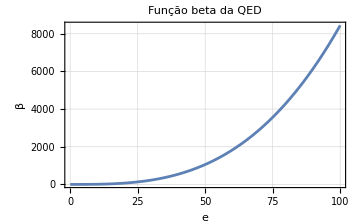

```mathematica
plot1=Plot[βQED[e],{e,0,100},Frame->True,FrameLabel->{"e","β"},LabelStyle->Directive[Bold, 10],Ticks->Automatic,ImageSize->Medium,GridLines->Automatic,PlotLabel->"Função beta da QED"]
```

```mathematica
plot2=Manipulate[{Plot[βQCD[g]/.{ns->0,nf->nff},{g,0,100},Frame->True,FrameLabel->{"g","β"},LabelStyle->Directive[Bold, 10],Ticks->Automatic,ImageSize->Medium,GridLines->Automatic,PlotLabel->"Função beta da QCD"],Subscript[n, f]==+nff},{{nff,8},1,20,1}]
```

onde n_s é o número de bósons com cor e n_f o número de sabores (flavors) da teoria. É possível ver o comportamento da Liberdade Assintótica,  já conhecido da QCD, onde o acoplamento tende a diminuir com a escala de energia (pelo menos para um número de sabores ≤16).

*Implementações com o pacote FeynRules serão formuladas em futuras atualizações